# Detecting patterns with Mathematica

## Observations and issues

Ivanov Denis  
ivanovdenis710616@gmail.com

Here the specific question is examined -  problems with FindGeometricTransform application and attempts to solve them.
But also this is preliminary material for a more serious study: counting stable centroidal Voronoi tesselations,
which I plan to propose later.

Notebook contains not only results, but also hot questions.  
So any help and comments are very appreciated!

November 2023

## Introduction

If you give a child or person far from mathematics the task: 
   place N centers uniformly in a square (or disk) 
then most likely the drawings will be about the following:

-Graphics-

and will be very similar to s.c. stable centroidal Voronoi tesselations (SCVT)
Unfortunately the article in wiki is a stub and contains an extra diagram that is not stable CVT.
Another method of obtaining such centroids (which often serves as an initialization for SCVT) 
is K-Means clustering. This is the method we will use here to get patterns.
Important point: if we running clustering several times with different initial conditions, 
we will get different results.  The same applies to SCVT search.
Let’s run example of K-Means clustering for a big set of random points in square.
How many different diagrams did you count?

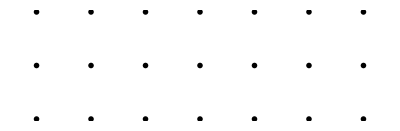

```mathematica
(*Evaluation time ~ 10 s *)
numSeeds=7;numTries=21;δ=0.01;
Subscript[ex, 0]=dataClust[numSeeds,δ,numTries,"Square"];
tinyPlots[Subscript[ex, 0],"Square",60,7]
```

In detail the issue of counting I hope to consider in another post. 
Here we will focus on the problem of selecting really different patterns.

#### Technical details

Initialization

All important functions are included in Code cells, which are running at the start of the notebook.

Run Input

Input cells that are marked LightPink color must be executed before the subsequent cells

(for collecting data). Other cells are independent.

Cells that will run long enough have Monitor option or/and commented with approximate timing.

### What is different and equal?

It’s rather of a philosophical question that’s often ironic )

-Graphics-
Undoubtedly, the capacity of brain’s working memory plays a role. 
You notice it easily, trying to choose the eye similar structures of patterns.

But in order to automate the pattern counting, we need a math criterion! 
As is often the case, it is very difficult to do it in a general way, for any shapes and dimensions 
(and imho in that much the difficulty of creating an effective FGF).
Here we consider two examples - a square and a disk. 
But on the basis of them it is possible to draw general conclusions.

## Square patterns

### Sameness criterion

Intuitively, it is clear that the equal patterns of centroids in the square 
must be invariants of the so-called dihedral group
- Wiki 2
- Wolfram demonstrations
This group has 3 generators: 
- Identity ℯ
- Rotation by 90° counterclockwise  𝒶
- Reflection  about the diagonal joining vertices “2” and “4”  𝓍
and 8 independent elements  {ℯ,𝒶,𝒶^2,𝒶^3,𝓍,𝒶𝓍,𝒶^2 𝓍,𝒶^3 𝓍}
If two patterns mapped by any of these elements, they are equal as centroids of the square.

```mathematica
Clear[dihedralTrans,transTypes];
dihedralTrans = Join[
	RotationTransform[#] & /@ {2 π, π/2, π, -π/2}, 
	ReflectionTransform[#] & /@ {{-1, 1}, {1, 0}, {1, 1}, {0, 1}}
	];
transTypes=MapThread[Rule[#1,#2]&,{dihedralTrans, {"ℯ","𝒶","𝒶^2","𝒶^3","𝓍","𝒶 𝓍","𝒶^2𝓍","𝒶^3𝓍"}}];
```

Interactive Illustrations

```mathematica
Manipulate[
	Graphics[GeometricTransformation[Text[Style["F",Bold,60]],
Composition[Sequence@@If[d=={},{dihedralTrans⟦1⟧},d]]],ImageSize->100],
	{{d,{dihedralTrans⟦1⟧},"Elems"},transTypes,ControlType->TogglerBar},
	ControlPlacement->Left, SaveDefinitions->True]
```

If patterns that equal in respect of dihedral group were exactly the same, it would be easy to gather it.
The difficulty is that clustering (like Lloyd’ relaxation for SCVT) always has some dispersion.
So let’s try to determine the distance function between any two patterns.

Firstly define custom distance function between sets of points in Euclidean space. 
It can be done in many ways, here is one of the effective:

This functions is universal for both square and disk.
They both have fundamentally similar results, but there’s an observation
which is preferable to Total for final selection of distinct patterns.

```mathematica
Clear[arrDistC,arrDistCTot];
arrDistC = Compile[{{arr1,_Real,2},{arr2,_Real,2}},
	(nf=Nearest[arr1];Max[SquaredEuclideanDistance[First@nf@#,#]&/@arr2])];
arrDistCTot = Compile[{{arr1,_Real,2},{arr2,_Real,2}},
	(nf=Nearest[arr1];Total[SquaredEuclideanDistance[First@nf@#,#]&/@arr2])];
```

And next we shall find for one of them all 8 transformations of dihedral group, 
and calculate the minimum arrDistC from them to another .

```mathematica
Clear[patternDistSquare,patternDistSquareTot];
patternDistSquare[arr1_,arr2_]:=With[{trans = Through[dihedralTrans[arr2]]}, 
	Min[arrDistC[arr1,#]&/@trans]]/;MatrixQ[arr1,NumericQ]&&MatrixQ[arr2,NumericQ];
patternDistSquareTot[arr1_,arr2_]:=With[{trans = Through[dihedralTrans[arr2]]}, 
	Min[arrDistCTot[arr1,#]&/@trans]]/;MatrixQ[arr1,NumericQ]&&MatrixQ[arr2,NumericQ];
```

Let’s start the experiment and get many enough examples of clustering centroids.

If you are sure and know the characteristics of your computer, run additional kernels.
Calculations will speed up proportionally, even without using Parallel (for versions 12+)

```mathematica
LaunchKernels[5];
```

Parameters:
  numSeeds : number of centroids
  numTries :   number of runnings with different random initial points
 δ :                    average distance between sampling points

```mathematica
(*Evaluation time ~ 2*10^-3 * numSeeds * numTries / δ s *)
numSeeds=11;numTries=100;δ=0.01;
dataSquare=dataClust[numSeeds,δ,numTries,"Square"];
```

```mathematica
tinyPlots[dataSquare[[1;;21]],"Square"]
```

```mathematica
regionPlots[dataSquare[[1;;10]],"Square"]
```

### Problem with FindGeometricTransform

Mathematica has an interesting function: FindGeometricTransform, that would be very useful in this case.
But my observations show that it often does not work correctly.
I created a post on Mathematica SE and a request for Wolfram Technical Support (ID [CASE:5082871] ).
They told me that:
...It does appear that FindGeometricTransform fails to find global minima your 2-dimensional case.
I have forwarded an issue report to our developers with the information you provided.
This is another example of the failure of  FGF, so we can’t use it for a while (

#### Example

```mathematica
Subscript[ex, 11]=;Subscript[ex, 12]=;
Column[{Row[{tinyPlots[{Subscript[ex, 11],Subscript[ex, 12]},"Square"]}],
Row[{FindGeometricTransform[Subscript[ex, 11],Subscript[ex, 12]],"  arrDist=",patternDistSquare[Subscript[ex, 11],Subscript[ex, 12]]}]}]
```

### Possible solutions for square

#### Clusterization

For small samples, we can use FindClusters with DistanceFunction → patternDistSquare 
with an undetermined number of clusters. But it works with reasonable time only  for 20-30 numTries.
And it takes hundreds or even thousands to get all SCVT.
Maybe I’m doing something wrong, I’d appreciate some advice!

```mathematica
lstSquareClust=First/@FindClusters[dataSquare, DistanceFunction->patternDistSquare,
PerformanceGoal->"Speed"];
```

```mathematica
tinyPlots[lstSquareClust,"Square"]
```

```mathematica
cc=ClusterClassify[dataSquare, DistanceFunction->patternDistSquare,
PerformanceGoal->"Speed"]
```

#### Gathering

Let’s try Gather function. The main thing is that in this case we can clearly define the threshold 
at which patterns are considered the same (in FindClusters this is done hiddenly).
Fortunately DistanceMatrix is very optimized in speed and memory.
After calculating it, we can see how the different distances between the patterns are distributed:

```mathematica
(*Evaluation time ~ numTries/20*)
dmSquare=DistanceMatrix[dataSquare,DistanceFunction->patternDistSquare,
PerformanceGoal->"Speed"];
```

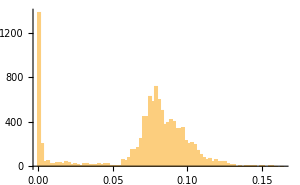

```mathematica
dataDistSquare=Flatten@Table[Drop[dmSquare⟦r⟧,r],{r,numTries}];
histDistSquare = Histogram[dataDistSquare,{0.002}, ImageSize->300]
```

Here we see s.c. multimodal distribution with main peaks near 0 (for probably equal patterns) and to the right - for distinct.
This is an interesting topic for detailed consideration.

Look at histograms depending on density of sampling points:

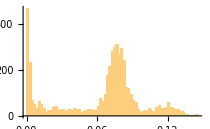
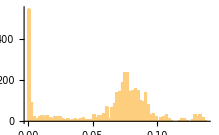
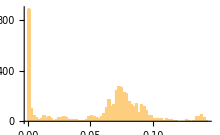
numSeeds = 11, numTries = 100
δ = 0.02:
-Graphics-
δ = 0.01
-Graphics-
δ = 0.005
-Graphics-

We see that the distributions are becoming more separated,but there is no clear empty interval as natural threshold.
So we have to choose a custom way to define it.
There are various separation criteria that are implemented in Mathematica 
as FindThreshold (with Otsu’s algorithmas default):

```mathematica
Subscript[σ, SqFT]=FindThreshold[dataDistSquare]
```

0.0449848

Let’s see what’s going on interactively:

```mathematica
Manipulate[
Row[{
Show[histDistSquare,GridLines->{{{σ,Directive[Red,Thick]}},None}],
Show[tinyPlots[dataSquare⟦First/@Gather[Range@numTries,(dmSquare⟦#1,#2⟧<σ)&]⟧ ,"Square",40,5],ImageSize->300]}],
{{σ,Subscript[σ, SqFT]},δ,Max@dataDistSquare,δ},
ControlPlacement->Top,ContinuousAction->False,SaveDefinitions->True]
```

Sadly there is strong suspicion that using σ_SqFT we may lose some unique patterns.
The minimum threshold is obviously δ.
Since I don’t see any other way not to lose patterns, set the threshold to δ 
and then do a detailed analysis.

```mathematica
resGatherSquare=dataSquare⟦First/@Gather[Range@numTries,(dmSquare⟦#1,#2⟧≤δ)&]⟧;
tinyPlots[resGatherSquare,"Square",60,7]
```

#### Final analysis

If you look closely at the patterns (for numSeeds = 11 they will be about 10), 
you can decide to combine some into one class.
This is a highly subjective process that cannot be fully automated.
However, Mathematica’s functions like ClusteringTree and Dendrogram make 
the final analysis convenient and visual.
Result is available as global variable finalResSquare.

For easy comparison of patterns in the cluster, 
let’s make alignment function:
convert them all into the form closest to the first.

```mathematica
Clear[alignPattsSquare];
alignPattsSquare[arr_]:=
  First@MinimalBy[Through[dihedralTrans[#]], arrDistCTot[#,First@arr]&]&/@arr;
```

#### Dendrogram

By changing interclusters distance h we will get different variants of classification of patterns as distinct.
You can also try various options for ClusterDissimilarityFunction.

```mathematica
lenSquare=Length@resGatherSquare;
rSquare=Range@lenSquare;
ctInitSquare=ClusteringTree[resGatherSquare->rSquare, 
DistanceFunction->patternDistSquareTot];
maxhSquare=Max[AnnotationValue[ctInitSquare,VertexWeight]];
finalResSquare={};

Manipulate[
ct=ClusteringTree[resGatherSquare->rSquare, 
h,DistanceFunction->patternDistSquareTot];
v=Values@AnnotationValue[ct,"LeafLabels"];
If[Length@v==1,v={rSquare}];
ap=alignPattsSquare/@(resGatherSquare⟦#⟧&/@v);
finalResSquare=ap⟦All,1⟧;
Row[{
Dendrogram[ctInitSquare, Axes->{False,True}, AxesOrigin->{0,0},
ImageSize->30 lenSquare,
Epilog->{Red,Line[{{0,h},{100,h}}]}],
Spacer[30],
Column[{Row[{"Distinct: ",Length@v}],
Manipulate[tinyPlots[ap⟦n⟧,"Square",50,5],
{n,Range@Length@v,ControlType->Setter},
ControlPlacement->Top,
SaveDefinitions->True]
}]
}]
,{h, δ,maxhSquare,δ,ControlPlacement->Top},
SaveDefinitions->True
]
```

```mathematica
Dynamic[tinyPlots[finalResSquare,"Square",50,8]]
```

## Disk patterns

### Creating possible sets

Start is similar to square:

```mathematica
LaunchKernels[5];
```

```mathematica
numSeeds=16;numTries=50;δ=0.01;
dataDisk=dataClust[numSeeds,δ,numTries,"Disk"];
```

```mathematica
tinyPlots[dataDisk⟦1;;21⟧,"Disk"]
```

```mathematica
regionPlots[dataDisk[[1;;10]],"Disk"]
```

Two important notes for disk:

Patterns with the same structure differ only with respect to rotation

But the angle of rotation may be any from 0 to 2 π (circle group)

### FGF

Unfortunately also failed (

```mathematica
Subscript[ex, 21]=;Subscript[ex, 22]=;
Column[{Row[{tinyPlots[{ex1,ex2},"Disk"]}],
Row[{FindGeometricTransform[Subscript[ex, 21],Subscript[ex, 22]],"  but arrDist = ",arrDistC[Subscript[ex, 21],RotationTransform[3.66]@Subscript[ex, 22]]}]}]
```

### Possible solutions

#### Direct minimization

To identify equal disk patterns, we may try to find rotation angle at which the distance between the sets of centroids is minimal.
NMinimize is designed for this, but its use causes difficulties. It is easy to understand why.
Enter the function of the distance between the sets depending on the angle of rotation:

```mathematica
Clear[patternDistθDisk];
patternDistθDisk[arr1_,arr2_,angle_]:=arrDistC[arr1, RotationTransform[angle]@arr2]/;
  MatrixQ[arr1,NumericQ]&&MatrixQ[arr2,NumericQ]&&NumericQ[angle];
```

and look of it’s plots

Examples for numSeeds = 5

```mathematica
Subscript[ex, 31]=;Subscript[ex, 32]=;Subscript[ex, 33]=;
```

```mathematica
Plot[{patternDistθDisk[Subscript[ex, 31],Subscript[ex, 32],θ],patternDistθDisk[Subscript[ex, 31],Subscript[ex, 33],θ]},{θ,0,2π},
PlotLegends->{tinyPlots[{Subscript[ex, 31],Subscript[ex, 32]},"Disk"],tinyPlots[{Subscript[ex, 31],Subscript[ex, 33]},"Disk"]}]
```

Examples for numSeeds = 14

```mathematica
Subscript[ex, 41]=;Subscript[ex, 42]=;Subscript[ex, 43]=;
```

```mathematica
Plot[{patternDistθDisk[Subscript[ex, 41],Subscript[ex, 43],θ],patternDistθDisk[Subscript[ex, 41],Subscript[ex, 42],θ]},{θ,0,2π},
PlotLegends->{tinyPlots[{Subscript[ex, 41],Subscript[ex, 43]},"Disk"],tinyPlots[{Subscript[ex, 41],Subscript[ex, 42]},"Disk"]}]
```

Obviously for such a complex goal function there will problems with NMinimize.
I’ve done a lot of experiments:
- tried different forms of arrDist
- tried many methods and options for NMinimize
Finally Method → {“RandomSearch”,”SearchPoints”→20/100} works well enough; 
but not always find a global minimum and take ~ 1 s for pattern what is very slow.
May be I mess something and need help!

```mathematica
Timing[NMinimize[{patternDistθDisk[Subscript[ex, 41],Subscript[ex, 42],θ],0≤θ≤2 π},θ,
Method->{"RandomSearch","SearchPoints"->100}]]
```

#### Trick with Polar coordinates

Let’s try to convert data to polar coordinates and enter specific functionы for rotation and
distances:

```mathematica
Clear[myFPC,polarRotateC,polarDistC,polarRotDist];
myFPC[{r_,θ_}]:={r Cos[θ], r Sin[θ]};
polarRotateC = Compile[{{arr,_Real,2},{θ,_Real}},{#[[1]],Mod[#[[2]]+θ,2π]}&/@arr];
polarDistC = Compile[{{arr1,_Real,2},{arr2,_Real,2}},
	Max[Min/@DistanceMatrix[arr1,arr2, DistanceFunction->ChessboardDistance]]];
polarDistCTot = Compile[{{arr1,_Real,2},{arr2,_Real,2}},
	Total[Min/@DistanceMatrix[arr1,arr2, DistanceFunction->ChessboardDistance]]];
polarRotDist[arr1_,arr2_,θ_]:=polarDistC[arr1, polarRotateC[arr2,θ]]/;
	MatrixQ[arr1,NumericQ]&&MatrixQ[arr2,NumericQ]&&NumericQ[θ];
```

```mathematica
dataPolar=SortBy[polarRotateC[#,2π],First]&/@ToPolarCoordinates[dataDisk];
```

Goal function looks complex also:

```mathematica
{Subscript[pex, 41],Subscript[pex, 42],Subscript[pex, 43]}=SortBy[polarRotateC[#,2π],First]&/@ToPolarCoordinates[{Subscript[ex, 41],Subscript[ex, 42],Subscript[ex, 43]}];
```

```mathematica
Plot[{polarRotDist[Subscript[pex, 41],Subscript[pex, 42],θ],polarRotDist[Subscript[pex, 41],Subscript[pex, 43],θ]},{θ,0,2π},
PlotLegends->{tinyPlots[{Subscript[ex, 41],Subscript[ex, 42]},"Disk"],tinyPlots[{Subscript[ex, 41],Subscript[ex, 43]},"Disk"]},PlotRange->{0,1}]
```

yet NMinimize now works ~10 times faster:

```mathematica
Timing[NMinimize[{polarRotDist[Subscript[pex, 41],Subscript[pex, 42],θ],0≤θ≤ 2 π},θ,
Method->{"RandomSearch","SearchPoints"->100}]]
```

but for many calculations still slow.

It remains to use bruteforce minimization: collect all values with step δ 
(which is obviously less than the interval localization of the minimum) and find Min.

```mathematica
Clear[patternDistPolar];
patternDistPolar[arr1_,arr2_]:=
  Min[polarDistC[arr1,polarRotateC[arr2,#]]&/@Range[0,2π,2 δ]]/;
	MatrixQ[arr1,NumericQ]&&MatrixQ[arr2,NumericQ];
	
patternDistPolarTot[arr1_,arr2_]:=
  Min[polarDistCTot[arr1,polarRotateC[arr2,#]]&/@Range[0,2π,2 δ]]/;
	MatrixQ[arr1,NumericQ]&&MatrixQ[arr2,NumericQ];
```

And in order not to make extra calculations get right here custom DistanceMatrix:

```mathematica
dataDistDisk={};
dmDisk=Array[0&,{numTries,numTries}];
Monitor[Do[
rotations=polarRotateC[dataPolar⟦i⟧,#]&/@ Range[0,2π,δ];
Do[
dist=Min[polarDistC[dataPolar⟦j⟧,#]&/@rotations];
AppendTo[dataDistDisk,dist];
dmDisk⟦i,j⟧=dmDisk⟦j,i⟧=dist
,{j,i+1,numTries}]
,{i,numTries}],i]
```

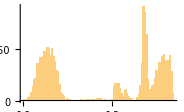
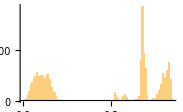
Next, all are similar to a square, but for relatively small numSeeds the distributions look much more separated, 
than for Cartesian coordinates:
numSeeds = 11, numTries = 100
δ = 0.02:
-Graphics-
δ = 0.01:
-Graphics-

```mathematica
histDistDisk=Histogram[dataDistDisk,{0.005},ImageSize->300]
```

So we can safely use

```mathematica
Subscript[σ, DskFT]=FindThreshold[dataDistDisk]
```

and gather using ready-made distance matrix:

```mathematica
resGatherDisk = dataPolar⟦First/@Gather[Range@numTries,(dmDisk⟦#1,#2⟧<Subscript[σ, DskFT])&]⟧;
```

```mathematica
tinyPlots[ Map[myFPC,resGatherDisk,{2}] , "Disk",50,5]
```

Just like for a square, at this selection we can be sure that we have not missed a single pattern.
But maybe some of them can be combined into one type.
In the end, the final decision is subjective and manual,
but we can create a basis for this with ClusteringTree and Dendrogram.

```mathematica
Clear[alignPattsDisk];
alignPattsDisk[arr_]:=Table[
  First@MinimalBy[
    polarRotateC[e,#]&/@ Range[0,2π,δ],
    polarDistCTot[#,First@arr]&],
 {e,arr}];
```

#### Final analysis with ClusteringTree and Dendrogram

```mathematica
lenDisk=Length@resGatherDisk;
rDisk=Range@lenDisk;
ctInitDisk=ClusteringTree[resGatherDisk->rDisk, 
DistanceFunction->patternDistPolarTot];
maxhDisk=Max[AnnotationValue[ctInitDisk,VertexWeight]];
finalResDisk={};

Manipulate[
ct=ClusteringTree[resGatherDisk->rDisk, 
h,DistanceFunction->patternDistPolarTot];
v=Values@AnnotationValue[ct,"LeafLabels"];
If[Length@v==1,v={rDisk}];
ap=alignPattsDisk/@(resGatherDisk⟦#⟧&/@v);
finalResDisk=ap⟦All,1⟧;
Row[{
Dendrogram[ctInitDisk, Axes->{False,True}, AxesOrigin->{0,0},
ImageSize->30 lenDisk,
Epilog->{Red,Line[{{0,h},{100,h}}]}],
Spacer[30],
Column[{Row[{"Distinct: ",Length@v}],
Manipulate[tinyPlots[Map[myFPC,ap⟦n⟧,{2}],"Disk",50,5],
{n,Range@Length@v,ControlType->Setter},
ControlPlacement->Top,
SaveDefinitions->True]
}]
}]
,{h,δ,maxhDisk,δ,
ControlPlacement->Top},
SaveDefinitions->True]
```

```mathematica
Dynamic[tinyPlots[Map[myFPC,finalResDisk,{2}],"Disk",50,8]]
```

## Code

### Patterns as K-Means clustering centroids

```mathematica
(*Regions: Global variable*)
Clear[regs]; regs=<|"Square"->Rectangle[{-1,-1},{1,1}],"Disk"->Disk[]|>;
Clear[dataClust];
dataClust[numSeeds_,δ_,numTries_,regID_]:=
With[{pts=RandomPoint[regs[regID],⌊8√2/δ^2⌋]},
	SeedRandom[];
	Reap[Monitor[
		Do[Sow[Mean/@FindClusters[pts,numSeeds,
			Method->{"KMeans",
			"InitialCentroids"-> RandomSample[pts,numSeeds]},
			PerformanceGoal->"Speed"]],
		{k,numTries}],
		ProgressIndicator[k,{1,numTries}]]]⟦2,1⟧]/;MemberQ[Keys[regs],regID];
```

### Voronoi

```mathematica
Clear[vMesh];
vMesh[pts_,regID_]:=With[{mesh=MeshPrimitives[VoronoiMesh[pts,{{-1,1},{-1,1}}],2]},
BoundaryDiscretizeRegion@RegionIntersection[#,regs[regID]]&/@mesh];
```

### Graphics

```mathematica
Clear[tinyPlots,tinyPlot,regionPlots];

tinyPlot[pts_,regID_,size_]:=
	Graphics[{FaceForm@White,EdgeForm@LightBlue,regs[regID],PointSize->0.07,GrayLevel[.2],Point@pts},
	ImageSize->size]/;MemberQ[Keys[regs],regID];

tinyPlots[lst_,regID_,size_,num_]:= GraphicsGrid[Partition[
	Graphics[{FaceForm@White,EdgeForm@LightBlue,regs[regID],PointSize->0.07,GrayLevel[.2],Point@#},
	ImageSize->size]&/@lst,UpTo[num]]]/;MemberQ[Keys[regs],regID];
	
regionPlots[lst_,regID_]:=With[{meshes=vMesh[#,regID]&/@lst,colors=Rescale[Range[Length@lst[[1]]]]},
 GraphicsGrid[Partition[Table[
    Graphics[{EdgeForm@Black,MapThread[{FaceForm[#1],#2}&, {ColorData["DarkBands"]/@colors,meshes⟦k⟧}],
	PointSize@.04,Point@lst⟦k⟧},ImageSize->80],{k,Length@lst}],
	UpTo[5]]]]/;MemberQ[Keys[regs],regID];
```